# μLang — Computationally Generating a Morphologically Average Conlang Lexicon from Multilingual Translations

Constructed languages, or conlangs, are languages that were artificially created instead of being naturally evolved over several generations. A crucial part of every conlang is the lexicon — the vocabulary. While most conlang lexicons are generated manually or through the help of randomized selection, I present several methods to generating a quantitatively “average” lexicon, that is, generating new words that may have similar features, spelling, or pronunciation compared to several translations of the same word in different languages.

## Initial Setup

I start with a simple word and and use translations provided by the Wolfram Language. In this case, I’m using “water”.

```mathematica
keyWord = "tiger";
```

Get the top 25 most spoken languages:

```mathematica
languages=EntityClass["Language",{"TotalSpeakers"->TakeLargest[100]}]//EntityList;
Iconize[languages, "List of languages"]
```

Get raw translations of our keyWord to the determined languages:

```mathematica
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation[keyWord, languages]];
rawTranslations//Short
```

{Chinese→虎,English→tiger,Mandarin Chinese→虎,Hindi→बाघ,Arabic→نِمر,Spanish→tigre,French→tigre,Standard Arabic→NotAvailable,Bengali→বাঘ,Russian→тигр,Portuguese→tigre,«78»,Afrikaans→tier,Southern Pashto→NotAvailable,Chhattisgarhi→NotAvailable,Rajasthani→NotAvailable,Cebuano→tigre,Mesopotamian Arabic→NotAvailable,Nigerian Fulfulde→NotAvailable,Assamese→বাঘ,Northeastern Thai→NotAvailable,Zhuang→NotAvailable,Northern Kurdish→NotAvailable}

Standardize all translated words — Transliterate to the Roman alphabet for easier string manipulation, ensure all words are lowercase, and remove translations that are not available.

```mathematica
translatedList=DeleteCases[DeleteDuplicates[ToLowerCase[Select[Transliterate[Values[rawTranslations]],StringMatchQ[#,CharacterRange["A","z"]..]&]]], "notavailable"]
```

{hu,tiger,bagha,nimr,tigre,tigr,harimau,chyta,chui,vagha,puli,kaplan,pali,ho,macan,seux,huli,tygrys,katuva,laofu,shyr,maung,agu,tigru,tijger,nahara,ingwe,shabeel,tier}

As a visual, I compared the edit distance between all pairs of multilingual words.

Compare the distance between every pair of words:

```mathematica
visualizeDistanceMatrix[wordList_]:=Module[{matrix,n},
n=Length[wordList];
matrix=Table[
EditDistance[wordList[[i]],wordList[[j]]],
{i,n},
{j,n}
];
ArrayPlot[matrix,ColorFunction->"Rainbow",PlotLabel->"Word Distance Matrix",ImageSize->{1200, 1200},FrameLabel->{"Words","Words"},PlotLegends->Automatic,FrameTicks->{Table[{i,wordList[[i]]},{i,n}],Table[{i,wordList[[i]]},{i,n}]}]]
```

Plot and visualize the distance matrix:

```mathematica
visualizeDistanceMatrix[translatedList]
```

-Graphics-

## Most Common Letter

Naturally, this is the very first idea I jumped to. I counted the most frequent letter at every index, found the average length of the original words, and concatenated the most common letters together.

Split each word into a List of characters:

```mathematica
charLists = Characters /@ translatedList;
charLists//Short
```

{{h,u},{t,i,g,e,r},{b,a,g,h,a},{n,i,m,r},{t,i,g,r,e},{t,i,g,r},«18»,{t,i,j,g,e,r},{n,a,h,a,r,a},{i,n,g,w,e},{s,h,a,b,e,e,l},{t,i,e,r}}

Find the average length of all words:

```mathematica
avgLen=Round[Mean[Length/@charLists]]
```

5

For words shorter in length than the average length, pad the List with dashes. For words longer than the average length, truncate the List accordingly:

```mathematica
augmentedLists=
Map[
Function[chars,
If[Length[chars]>avgLen,
Take[chars,avgLen],
PadRight[chars,avgLen,"-"]
]
],charLists];

augmentedLists//Short
```

{{h,u,-,-,-},{t,i,g,e,r},{b,a,g,h,a},{n,i,m,r,-},{t,i,g,r,e},{t,i,g,r,-},«18»,{t,i,j,g,e},{n,a,h,a,r},{i,n,g,w,e},{s,h,a,b,e},{t,i,e,r,-}}

Transpose the charList for easier calculation of the most frequent character at every position:

```mathematica
transposed=Transpose[augmentedLists];
```

Find the most frequency character at each position and generate the average word:

```mathematica
mostFreqChar=
Map[
If[
DeleteCases[#,"-"]==={},
"-",
First@First@SortBy[Tally@DeleteCases[#,"-"],-Last[#]&]]&,
transposed
];
```

```mathematica
mostFreqCharWord=StringJoin[DeleteCases[mostFreqChar,"-"]]
```

tagra

While this method does “work,” it doesn’t produce very creative words. It always outputs one very predictable word and there is no variance. To generate an exciting lexicon, I explored some other methods.

## Most Common Digram

My second approach was to split each word into digrams (pairs of consecutive letters) and find the most common digram in each position. Then, we can join the most common digrams together. For example, “su” is the first digram in “sun” and “un” is the second digram in “sun.”

Calculate the average syllable count:

```mathematica
SYLLABLECOUNT = Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
```

2

Split each word into digrams and record the position of each digram:

```mathematica
positionedDigrams=Flatten[
Table[
If[
StringLength[word]>=pos+1,
{pos,StringTake[word,{pos,pos+1}]},
Nothing],
{word,translatedList},
{pos,StringLength[word]-1}
],1];
positionedDigrams//Short
```

{{1,hu},{1,ti},{2,ig},{3,ge},{4,er},{1,ba},{2,ag},{3,gh},{4,ha},{1,ni},{2,im},{3,mr},{1,ti},{2,ig},«80»,{5,ra},{1,in},{2,ng},{3,gw},{4,we},{1,sh},{2,ha},{3,ab},{4,be},{5,ee},{6,el},{1,ti},{2,ie},{3,er}}

Group digrams by their position:

```mathematica
groupedByPosition=GroupBy[positionedDigrams,First->Last];
Iconize[groupedByPosition]
```

Count the frequency of each digram in each position:

```mathematica
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
countsByPosition//First
```

<|hu→2,ti→6,ba→1,ni→1,ha→1,ch→2,va→1,pu→1,ka→2,pa→1,ho→1,ma→2,se→1,ty→1,la→1,sh→2,ag→1,na→1,in→1|>

Get the most frequent digram in each position:

```mathematica
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[1]],{pos,Sort@Keys[countsByPosition]}]
```

{{ti},{ig},{gr},{ha},{ma},{au}}

Generate new words by combining the most frequent digrams:

```mathematica
generateWord[]:=Module[{numSyllables,selectedLists,syllables},
numSyllables:=RandomInteger[{Max[1, SYLLABLECOUNT-2], Min[Length[topDigramsByPosition], SYLLABLECOUNT+2]}];
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]
]
```

Generate the most

```mathematica
mostDigramGenerated=DeleteDuplicates[Table[generateWord[],{10}]]
```

{ti,tiig,tiiggr,tiiggrha}

This isn’t great either. While there are some pronounceable words, this method is very basic and relies on the most common digrams. In fact, both of the previous methods relied very strictly on the most frequent characters with extremely basic substitution algorithms.

## Genetic Evolution

A different approach is to imagine the original list of translated words as a base “population.” Through a genetic algorithm, we can “evolve” the population and generate new words that are similar but completely unique.

Define important variables. populationSize is the size of the population each generation and mutationRate:

```mathematica
Clear[populationSize, generations, mutationRate, topDigramsByPosition, fitnessFunction, population, randomString, allBest];
populationSize=100;
generations=5;
mutationRate=0.2;
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}]
allBest = {};
words = translatedList;
charSet = Flatten[topDigramsByPosition];
MAXLENGTH = Round[Mean[StringLength/@ words]]
allPopulations = {};
avgFitnessPerGen = {};
```

{{ti,hu,ch,ka,ma},{ig,ag,hy,ul,im},{gr,li,gh,ge,mr},{ha,er,re,im,ta},{ma,an,ys,va,er},{au,el}}

5

```mathematica
phoneticDifference[word1_String,word2_String]:=Module[{soundex1,soundex2},
soundex1=ResourceFunction["Soundex"][word1];
soundex2=ResourceFunction["Soundex"][word2];
If[soundex1===soundex2,0,EditDistance[soundex1,soundex2]]
];
```

Our fitness function will calculate weighted fitness score using the Levenshtein distance and phonetic distance between a candidate word and each word in the original word list:

```mathematica
fitnessFunction[candidate_String]:=Module[{maxEditDistance,maxPhoneticDistance,editScore,phoneticScore},
maxEditDistance=Max[EditDistance[candidate,#]&/@words];
maxPhoneticDistance=Max[phoneticDifference[candidate,#]&/@words];
editScore=If[maxEditDistance>0,1-N[Mean[EditDistance[candidate,#]&/@words]/maxEditDistance],1];
phoneticScore=If[maxPhoneticDistance>0,1-N[Mean[phoneticDifference[candidate,#]&/@words]/maxPhoneticDistance],1];
0.5*editScore+0.5*phoneticScore
];
```

The fitness of a word similar to possible keyWord translations is significantly greater than a completely unrelated fitness word:

```mathematica
fitnessFunction[WordTranslation[keyWord, "Spanish"][[1]]]
```

0.385057

```mathematica
fitnessFunction["random word"]
```

0.0552508

Here is our list of possible digrams:

```mathematica
charSet
```

{ti,hu,ch,ka,ma,ig,ag,hy,ul,im,gr,li,gh,ge,mr,ha,er,re,im,ta,ma,an,ys,va,er,au,el}

Create our original population by randomly combining digrams:

```mathematica
randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{SYLLABLECOUNT,SYLLABLECOUNT+2}]];
population=Table[randomString[],{populationSize}];
population
```

{ululys,agig,mrul,kali,aulierig,hygrhu,mrig,tiim,rehy,vati,vaag,yshyelan,vael,hytire,kaigchma,igtiim,maergr,makael,grimtagr,ervamrmr,igimerva,liim,elgeau,hahychha,kaerhamr,kaimelau,hyagel,mahaul,tita,talimrma,mran,imer,chvakaan,mamama,ghgh,ulagan,hukaim,reys,imghul,taer,grhu,mava,hamama,auerig,vareuler,titaelha,geau,grmrvaag,haerlier,magrhuer,grelan,haysmati,kava,imigmrim,rekaig,ermaan,mrre,ermaerti,tiau,tiim,geulel,haig,anmahaim,auchimka,hahuva,elghimhu,ligh,igli,agimgh,timrag,ghkaul,anmaulli,humrmays,liululhu,maultage,remrauma,vaelma,kaghrege,huanim,mrre,rechvaim,ermaighu,maigighu,ligr,erimag,mrer,ysti,hugehy,anva,vaelerge,taerhu,remaelag,timrmali,taghva,timr,mahughha,maer,elrere,huhugech,chreta}

With everything set up, I can simulate several hundred generations of evolution. I used a modified two-point crossover algorithm that allowed both parent words to vary in length.

Implementation of crossover:

```mathematica
lengthVaryTwoPointCrossover[p1_,p2_]:=Module[{len1,len2,minLen,pt1,pt2,c1,c2,child},
len1=StringLength[p1];
len2=StringLength[p2];
minLen=Min[len1,len2];
{pt1,pt2}=Sort@RandomSample[Range[minLen],2];
c1=Characters[p1];
c2=Characters[p2];
child=Join[Take[c1,pt1-1],Take[c2,{pt1,pt2}],Drop[c1,pt2]];
If[
Length[child]>
MAXLENGTH,
child=Take[child,MAXLENGTH]
];
StringJoin[child]];
```

Implementation of string mutation:

```mathematica
mutate[str_]:=StringJoin@
Table[
If[RandomReal[]<mutationRate,
RandomChoice[charSet],
c
],
{c,Characters[str]}
];
```

I record the best/”most fit” word each generation:

```mathematica
allBest=Table[fitnesses=fitnessFunction/@population;
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
avgF=N[Mean[fitnesses]];
AppendTo[avgFitnessPerGen,avgF];
AppendTo[allPopulations,population];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
population=Table[mutate@lengthVaryTwoPointCrossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];
bestCandidate,{gen,1,generations}
];

AppendTo[allPopulations,population];
```

The best performing strings in each generation:

```mathematica
allBest//Short
```

{ligh,tili,tili,tiys,tiyys}

Log the most fit string:

```mathematica
bestWordGeneticPool=First@MaximalBy[allBest,fitnessFunction];
Print["Best word found: ",bestWordGeneticPool];
Print["Fitness: ",fitnessFunction[bestWordGeneticPool]];
```

Best word found: tiys

Fitness: 0.462438

Plot the average fitness of every population of each generation over time:

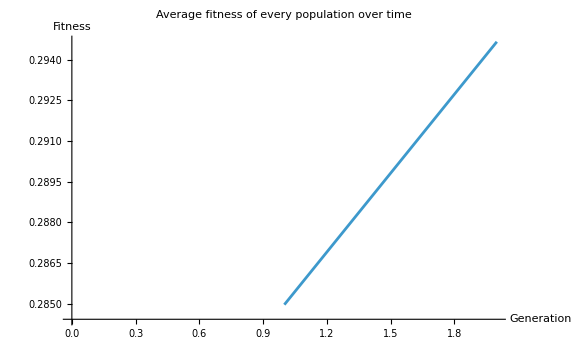

```mathematica
ListLinePlot[MovingAverage[avgFitnessPerGen,4],ImageSize->Large,PlotLabel->"Average fitness of every population over time",AxesLabel->{"Generation","Fitness"}]
```

Overall, there is a trend of increasing fitness throughout the graph. There are many fluctuations due to rando

## String Optimization

Linguistic evolution can also be viewed as an optimization problem. I want to continuously evolve a string to be have the lowest average edit distance to all the multilingual words. I take a string and evolve it through several hundred generations. Each generation, I evolve the string towards the multilingual word that is most different from it.

Set up basic variables:

```mathematica
Clear[baseWord, testList, padChar, baseWordStates, targetWords,GENERATIONS];
baseWord=StringJoin@RandomChoice[CharacterRange["a", "z"], 5];
startingWord = baseWord;
testList=translatedList
padChar="_";
baseWordStates={baseWord};
targetWords={};
GENERATIONS=1000;
averageLength=Round[Mean[StringLength /@ testList]];

getAllChars[wordList_]:=Module[{maxLen,paddedWords,allChars},
maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
allChars=Union[Flatten[Characters/@paddedWords]];
allChars
];

pad[w1_,w2_]:=Module[{maxLen,p1,p2},
maxLen=Max[StringLength[w1],StringLength[w2]];
{StringPadRight[w1,maxLen,padChar],StringPadRight[w2,maxLen,padChar]}
];

mostDifferentWord[base_,list_]:=Module[{diffs},diffs=Table[{word,EditDistance[base,word]},{word,list}];
First@MaximalBy[diffs,Last]];

findDifferingIndices[str1_,str2_]:=Module[{minLen,diffs},minLen=Min[StringLength[str1],StringLength[str2]];
diffs=Select[Range[minLen],StringTake[str1,{#}]=!=StringTake[str2,{#}]&];
diffs]

layoutTestWords[baseWord_, testList_] := 
  Module[{angles, positions}, 
   angles = Subdivide[0, 2*Pi, Length[testList]][[1 ;; -2]];
   positions = Table[
     With[{dist = EditDistance[baseWord, testList[[i]]]},
      {testList[[i]], 
       Cos[angles[[i]]]*dist, 
       Sin[angles[[i]]]*dist}
      ], {i, 1, Length[testList]}];
   positions];
```

{hu,tiger,bagha,nimr,tigre,tigr,harimau,chyta,chui,vagha,puli,kaplan,pali,ho,macan,seux,huli,tygrys,katuva,laofu,shyr,maung,agu,tigru,tijger,nahara,ingwe,shabeel,tier}

I assign a weight to each character based on its frequency. This way, I encourage evolving towards more frequent characters at any position.

Calculate character frequencies for each position:

```mathematica
calculateCharFrequencies[wordList_]:=Module[{maxLen,paddedWords,freqTables},
maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
freqTables=Table[Counts[StringTake[#,{pos}]&/@paddedWords],{pos,1,maxLen}];
freqTables
]
```

Normalize frequencies to a decimal number between 0 and 1:

```mathematica
normalizeFrequencies[freqTable_]:=Module[{nonZeroEntries,total},
nonZeroEntries=Select[freqTable,#>0&];
total=Total[Values[nonZeroEntries]];
If[
total==0,
freqTable,
Association[#->If[freqTable[#]>0,N[freqTable[#]/total],0]&/@Keys[freqTable]]
]
]
```

Calculate weighted character frequencies:

```mathematica
allPossibleChars=getAllChars[testList];
rawFrequencies=calculateCharFrequencies[testList];

charFreqWeights=Map[normalizeFrequencies[AssociationThread[allPossibleChars,Lookup[#,allPossibleChars,0]]]&,rawFrequencies];
```

Decide the character to evolve into based on the frequency weightings:

```mathematica
weightedRandomTarget[base_,list_]:=Module[{diffs,total,weights},
diffs=Table[{word,EditDistance[base,word]},{word,list}];
total=Total[diffs[[All,2]]];
If[total==0,

RandomChoice[list],
weights=(diffs[[All,2]]^3)/Total[diffs[[All,2]]^3];
RandomChoice[weights->diffs[[All,1]]]]
];
```

Mutate a character at randomly 5% of the time:

```mathematica
randomMutation[word_,rate_:0.05]:=Module[{chars,mutated},chars=Characters[word];
mutated=Map[If[RandomReal[]<rate,RandomChoice[CharacterRange["a","z"]~Join~{padChar}],#]&,chars];
StringJoin[mutated]];
```

Evolve towards the decided character:

```mathematica
evolveTowardWeighted[base_,target_]:=Module[{basePadded,targetPadded,diffIndices,i,targetChar,baseChar,weight},{basePadded,targetPadded}=pad[base,target];
diffIndices=findDifferingIndices[basePadded,targetPadded];
If[diffIndices==={},basePadded,
i=RandomChoice[diffIndices];
targetChar=StringTake[targetPadded,{i,i}];
baseChar=StringTake[basePadded,{i,i}];
weight=
If[
i<=Length[charFreqWeights],
chars=Keys[charFreqWeights[[i]]];
weights = Values[charFreqWeights[[i]]];
choice = RandomChoice[weights->chars];
StringReplacePart[basePadded, choice, {i, i}], basePadded]]];
```

Simulate hundreds of generations:

```mathematica
baseWordStates={baseWord};
targetWords={};
bestWord=baseWord;
bestDistance=Mean[EditDistance[baseWord,#]&/@testList];
evolutionStep[{currentWord_,currentBest_,bestDist_,targetHist_,stateHist_}]:=
Module[{target,newWord,newDist},
target=weightedRandomTarget[currentWord,testList];
newWord=StringReplace[evolveTowardWeighted[currentWord,target],"_"->""];
newDist=Mean[EditDistance[newWord,#]&/@testList
];
If[
newDist<bestDist,
{newWord,newWord,newDist,Append[targetHist,target],Append[stateHist,newWord]},
{newWord,currentBest,bestDist,Append[targetHist,target],Append[stateHist,newWord]}
]
];
initialState={baseWord,baseWord,Mean[EditDistance[baseWord,#]&/@testList],{},{baseWord}};
evolutionResults=NestList[evolutionStep,initialState,GENERATIONS];
{finalWord,bestWord,bestDistance,targetWords,baseWordStates}=Last[evolutionResults];


testPositions=layoutTestWords[baseWordStates[[1]],testList];
positionDict=Association[#[[1]]->{#[[2]],#[[3]]}&/@testPositions];
```

Generate animation:

```mathematica
createEvolutionAnimation[]:=Module[{frames,maxFrames,basePos={0,0},targetPos,newX,newY,t=0.25},maxFrames=Length[baseWordStates];
frames=Table[Module[{currentWord,target,bx,by,tx,ty},
currentWord=baseWordStates[[frame]];
If[frame<=Length[targetWords],target=targetWords[[frame]],target=targetWords[[-1]]];
targetPos=positionDict[target];
tx=targetPos[[1]];
ty=targetPos[[2]];
If[frame==1,{bx,by}={0,0},newX=basePos[[1]]+t*(tx-basePos[[1]]);
newY=basePos[[2]]+t*(ty-basePos[[2]]);
basePos={newX,newY};
{bx,by}=basePos;];
Show[Graphics[{Gray,Table[Text[Style[StringReplace[testPositions[[i,1]],"_"->""],FontSize->12],{testPositions[[i,2]],testPositions[[i,3]]}],{i,1,Length[testPositions]}],Red,Thickness[0.003],Line[{{bx,by},{tx,ty}}],Red,Text[Style[StringReplace[currentWord,"_"->""],FontSize->18,Bold],{bx,by}],Red,Text[Style["Target: "<>StringReplace[target,"_"->""],FontSize->12],{0,9.5}],Blue}],PlotRange->{{-10,10},{-10,10}},Axes->False,Frame->False,ImageSize->{400,400}]],{frame,1,maxFrames}];
ListAnimate[frames,AnimationRate->5,AnimationRepetitions->1]];

evolutionAnimation=createEvolutionAnimation[];
evolutionAnimation


bestWord=StringReplace[bestWord,"_"->""];
Print["Best word found: ",bestWord];
Print["Best average distance: ",N[bestDistance]];
```

Best word found: tagr

Best average distance: 3.55172

Plot the average word distance between the evolving string and multilingual word list over generations:

```mathematica
plotEvolutionProgress[baseWordStates_,testList_]:=Module[{distances,generations},distances=Table[Mean[EditDistance[baseWordStates[[i]],#]&/@testList],{i,1,Length[baseWordStates]}];
generations=Range[0,Length[baseWordStates]-1];
ListLinePlot[MovingAverage[Transpose[{generations,distances}], 3],PlotLabel->"Average Distance to Multilingual Wordlist (lower is better)",AxesLabel->{"Generation","Average Distance"},PlotStyle->{Red,Thick},GridLines->Automatic, AspectRatio->1, ImageSize->{550, 550}]]
```

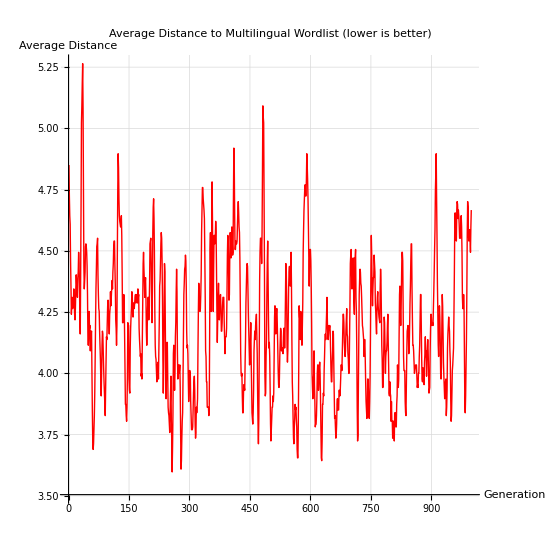

```mathematica
plotEvolutionProgress[baseWordStates, testList]
```

There is a weak decreasing trend in the average distance, showing a general improvement in evolution

## Generation with Morphological Neural Net Features

A more modern approach may be to take advantage of neural net embeddings. A neural net/deep learning model encodes words in a numeric representation called embeddings or feature vectors. For text, embeddings usually encode semantic meaning. We can ask the neural net to generate new words with similar embedding values as the training set (the original word list), generating new but similar words.

```mathematica
net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
```

NetGraph[…]

```mathematica
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
```

```mathematica
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]]
```

NetGraph[…]

```mathematica
results = 
 NetTrain[net, <|"Input" -> translatedList|>, All, LossFunction -> "Loss",   MaxTrainingRounds ->500]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:500  rounds:500  time:15s  examples/s:969
data | ,,  training examples:29  processed examples:14500  skipped examples:0
method | ,,  ADAMoptimizer  batch size29CPU
round | ,,  loss:6.21×10^-1  error:25.2%
 | 
 | ]

```mathematica
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}]
```

NetChain[<3>]

```mathematica
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
```

```mathematica
newAvgWords=Sort@Complement[Table[wordz[],15],translatedList]
```

{hoi,hui,ingw,kapl,katu,maun}

```mathematica
extractor=NetChain[{trainednet,AggregationLayer[Max,1]}]
```

NetChain[<2>]

```mathematica
allPossibleWords = Flatten[Join[{newAvgWords, bestWordGeneticPool, mostDigramGenerated,
     mostFreqCharWord, bestWord}]]
```

{hoi,hui,ingw,kapl,katu,maun,tiys,ti,tiig,tiiggr,tiiggrha,tagra,tagr}

## Generation with Phonetic Neural Net Features

I also apply the same neural net pipeline for multilingual words converted into the International Phonetic Alphabet (IPA).

Initialize the neural network:

```mathematica
netPhon=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
```

NetGraph[…]

Because this network can only accept Roman letters, numerals, and punctuation, I map the IPA symbols to numbers and punctuation that is not contained .

Set up the mapping association:

```mathematica
symbolMap=<|"θ"->"1","ð"->"2","ʃ"->"3","ʒ"->"4","ɪ"->"5","ɛ"->"6","æ"->"7","ɔ"->"8","ʊ"->"9","ʌ"->"0","ə"->".","ɜ"->",","ŋ"->";","ɡ"->":","ɑ"->"!" ,"ˈ"->"@", "ˌ"->"=", "ɒ"->"*", "ɝ"->"["|>
```

<|θ→1,ð→2,ʃ→3,ʒ→4,ɪ→5,ɛ→6,æ→7,ɔ→8,ʊ→9,ʌ→0,ə→.,ɜ→,,ŋ→;,ɡ→:,ɑ→!,ˈ→@,ˌ→=,ɒ→*|>

```mathematica
ipaList=ResourceFunction["WordPhoneticSyllabify"][#][[2]]&/@translatedList;
```

```mathematica
convertedTrainList = StringJoin[Lookup[symbolMap,#,#]&/@Characters[#]]&/@StringReplace[ipaList, "•"->""];
```

```mathematica
convertedTrainList
```

{hoo,taher,b@7:h.,n5mɝ,t@i:re5,ta5:.r,h@!r5ma9,k@a5t.,kooi,v@!:.,p@uli,kapluhn,p@!li,hoh,m@7k.n,s@uks,h@uli,t@a5:r5s,k.@tuv.,l@a9fu,3a5r,mawn,7@:u,t5@:ru,t@a5:.r,n.@h!r.,5;@:we5,3.@bil,teer}

```mathematica
ipaList[[4]]
```

nɪ•mɝ

```mathematica
vocabularyPhon=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}•"];
```

```mathematica
netPhon=NetReplacePart[netPhon,"Input"->NetEncoder[{"Characters",{vocabularyPhon,{StartOfString,EndOfString}->97}}]]
```

NetGraph[…]

```mathematica
resultsPhon = 
 NetTrain[netPhon, <|"Input" -> convertedTrainList|>, All, LossFunction -> "Loss",  MaxTrainingRounds ->500]
```

NetTrain::encgenfail1: Could not encode training input number 4 for port "Input": input string contained unkown characters and the encoder doesn't contain _ in the character list. Please check the example.

$Failed

```mathematica
trainednetPhon=resultsPhon["TrainedNet"];
generatorPhon=NetReplacePart[NetExtract[trainednetPhon,"predict"],{"Input"->NetEncoder[{"Characters",{vocabularyPhon,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabularyPhon,""]}]}]
```

NetExtract::arg1: First argument $Failed[TrainedNet] should be a net, NetEncoder, or NetDecoder.

NetReplacePart::netarg1: First argument should be a valid net.

$Failed

```mathematica
wordzPhon[]:=With[{obj=NetStateObject[generatorPhon]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
```

```mathematica
newAvgWordsPhonetics=StringJoin[Lookup[Association[Reverse /@ Normal[symbolMap]],#,#]&/@Characters[#]]&/@Sort@Complement[DeleteDuplicates[Table[wordzPhon[],15]], convertedTrainList]
```

NetStateObject::arg1: First argument to NetStateObject should be a valid net.

StringJoin::string: String expected at position 1 in $Failed[Last[{,}],RandomSample]<>$Failed[Last[$Failed[Last[{,}],RandomSample]],RandomSample]<>$Failed[Last[$Failed[Last[$Failed[Last[{«2»}],RandomSample]],RandomSample]],RandomSample]<>$Failed[Last[$Failed[Last[$Failed[Last[$Failed[«2»]],RandomSample]],RandomSample]],RandomSample].

StringJoin::string: String expected at position 2 in $Failed[Last[{,}],RandomSample]<>$Failed[Last[$Failed[Last[{,}],RandomSample]],RandomSample]<>$Failed[Last[$Failed[Last[$Failed[Last[{«2»}],RandomSample]],RandomSample]],RandomSample]<>$Failed[Last[$Failed[Last[$Failed[Last[$Failed[«2»]],RandomSample]],RandomSample]],RandomSample].

StringJoin::string: String expected at position 3 in $Failed[Last[{,}],RandomSample]<>$Failed[Last[$Failed[Last[{,}],RandomSample]],RandomSample]<>$Failed[Last[$Failed[Last[$Failed[Last[{«2»}],RandomSample]],RandomSample]],RandomSample]<>$Failed[Last[$Failed[Last[$Failed[Last[$Failed[«2»]],RandomSample]],RandomSample]],RandomSample].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

NetStateObject::arg1: First argument to NetStateObject should be a valid net.

General::stop: Further output of NetStateObject::arg1 will be suppressed during this calculation.

{StringJoin[Characters[$Failed[Last[{,}],RandomSample]<>$Failed[Last[$Failed[Last[{,}],RandomSample]],RandomSample]<>$Failed[Last[$Failed[Last[$Failed[Last[{,}],RandomSample]],RandomSample]],RandomSample]<>$Failed[Last[$Failed[Last[$Failed[Last[$Failed[Last[{,}],RandomSample]],RandomSample]],RandomSample]],RandomSample]]]}

```mathematica
extractorPhon=NetChain[{trainednetPhon,AggregationLayer[Max,1]}]
```

NetChain::netinvnodes: $Failed[TrainedNet] is not a layer, a net, or a valid specification for one.

$Failed

```mathematica
newAvgWordsPhonetics
```

{StringJoin[Characters[$Failed[Last[{,}],RandomSample]<>$Failed[Last[$Failed[Last[{,}],RandomSample]],RandomSample]<>$Failed[Last[$Failed[Last[$Failed[Last[{,}],RandomSample]],RandomSample]],RandomSample]<>$Failed[Last[$Failed[Last[$Failed[Last[$Failed[Last[{,}],RandomSample]],RandomSample]],RandomSample]],RandomSample]]]}

## Graphical Interface

```mathematica
DynamicModule[{keyWord="sun",mostFreqCharWord="",mostDigramGenerated={},SYLLABLECOUNT=0,bestWordGeneticPool="",bestWord="",newAvgWords={}},Panel[Column[{Style["μLang Lexicon Generator",Bold,14],Row[{"Enter keyword: ",InputField[Dynamic[keyWord],String]}],Button["Generate",Module[{languages,rawTranslations,translatedList,charLists,avgLen,augmentedLists,transposed,mostFreqChar,positionedDigrams,groupedByPosition,countsByPosition,topDigramsByPosition,generateWord,populationSize,generations,mutationRate,fitnessFunction,population,randomString,allBest,words,charSet,MAXLENGTH,allPopulations,avgFitnessPerGen,phoneticDifference,bestCandidate,fitnesses,parents,baseWord,testList,padChar,baseWordStates,targetWords,GENERATIONS,averageLength,allPossibleChars,rawFrequencies,charFreqWeights,initialState,evolutionResults,finalWord,bestDistance,testPositions,positionDict,net,vocabulary,results,trainednet,generator,wordz},(*---Translation& Preprocessing---*)languages=EntityClass["Language",{"TotalSpeakers"->TakeLargest[100]}]//EntityList;
rawTranslations=KeyValueMap[#1->First[#2]&,WordTranslation[keyWord,languages]];
translatedList=DeleteCases[DeleteDuplicates[ToLowerCase[Select[Transliterate[Values[rawTranslations]],StringMatchQ[#,CharacterRange["A","z"]..]&]]],"notavailable"];


charLists=Characters/@translatedList;
avgLen=Round[Mean[Length/@charLists]];
augmentedLists=Map[Function[chars,If[Length[chars]>avgLen,Take[chars,avgLen],PadRight[chars,avgLen,"-"]]],charLists];
transposed=Transpose[augmentedLists];
mostFreqChar=Map[If[DeleteCases[#,"-"]==={},"-",First@First@SortBy[Tally@DeleteCases[#,"-"],-Last[#]&]]&,transposed];
mostFreqCharWord=StringJoin[DeleteCases[mostFreqChar,"-"]];
SYLLABLECOUNT=Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]];


positionedDigrams=Flatten[Table[If[StringLength[word]>=pos+1,{pos,StringTake[word,{pos,pos+1}]},Nothing],{word,translatedList},{pos,StringLength[word]-1}],1];
groupedByPosition=GroupBy[positionedDigrams,First->Last];
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[1]],{pos,Sort@Keys[countsByPosition]}];
generateWord[]:=Module[{numSyllables,selectedLists,syllables},numSyllables=RandomInteger[{Max[1,SYLLABLECOUNT-2],Min[Length[topDigramsByPosition],SYLLABLECOUNT+2]}];
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]];
mostDigramGenerated=DeleteDuplicates[Table[generateWord[],{10}]];


populationSize=100;
generations=5;
mutationRate=0.2;
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}];
allBest={};
words=translatedList;
charSet=Flatten[topDigramsByPosition];
MAXLENGTH=Round[Mean[StringLength/@words]];
allPopulations={};
avgFitnessPerGen={};
phoneticDifference[word1_String,word2_String]:=Module[{soundex1,soundex2},soundex1=ResourceFunction["Soundex"][word1];
soundex2=ResourceFunction["Soundex"][word2];
If[soundex1===soundex2,0,EditDistance[soundex1,soundex2]]];
fitnessFunction[candidate_String]:=Module[{maxEditDistance,maxPhoneticDistance,editScore,phoneticScore},maxEditDistance=Max[EditDistance[candidate,#]&/@words];
maxPhoneticDistance=Max[phoneticDifference[candidate,#]&/@words];
editScore=If[maxEditDistance>0,1-N[Mean[EditDistance[candidate,#]&/@words]/maxEditDistance],1];
phoneticScore=If[maxPhoneticDistance>0,1-N[Mean[phoneticDifference[candidate,#]&/@words]/maxPhoneticDistance],1];
0.5*editScore+0.5*phoneticScore];
randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{SYLLABLECOUNT,SYLLABLECOUNT+2}]];
population=Table[randomString[],{populationSize}];
lengthVaryTwoPointCrossover[p1_,p2_]:=Module[{len1,len2,minLen,pt1,pt2,c1,c2,child},len1=StringLength[p1];
len2=StringLength[p2];
minLen=Min[len1,len2];
{pt1,pt2}=Sort@RandomSample[Range[minLen],2];
c1=Characters[p1];
c2=Characters[p2];
child=Join[Take[c1,pt1-1],Take[c2,{pt1,pt2}],Drop[c1,pt2]];
If[Length[child]>MAXLENGTH,child=Take[child,MAXLENGTH]];
StringJoin[child]];
mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];
allBest=Table[fitnesses=fitnessFunction/@population;
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
AppendTo[avgFitnessPerGen,N[Mean[fitnesses]]];
AppendTo[allPopulations,population];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
population=Table[mutate@lengthVaryTwoPointCrossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];
bestCandidate,{gen,1,generations}];
AppendTo[allPopulations,population];
bestWordGeneticPool=First@MaximalBy[allBest,fitnessFunction];


baseWord=StringJoin@RandomChoice[CharacterRange["a","z"],5];
testList=translatedList;
padChar="_";
baseWordStates={baseWord};
targetWords={};
GENERATIONS=1000;
averageLength=Round[Mean[StringLength/@testList]];
getAllChars[wordList_]:=Module[{maxLen,paddedWords,allChars},maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
allChars=Union[Flatten[Characters/@paddedWords]];
allChars];
pad[w1_,w2_]:=Module[{maxLen,p1,p2},maxLen=Max[StringLength[w1],StringLength[w2]];
{StringPadRight[w1,maxLen,padChar],StringPadRight[w2,maxLen,padChar]}];
mostDifferentWord[base_,list_]:=Module[{diffs},diffs=Table[{word,EditDistance[base,word]},{word,list}];
First@MaximalBy[diffs,Last]];
findDifferingIndices[str1_,str2_]:=Module[{minLen,diffs},minLen=Min[StringLength[str1],StringLength[str2]];
diffs=Select[Range[minLen],StringTake[str1,{#}]=!=StringTake[str2,{#}]&];
diffs];
layoutTestWords[baseWord_,testList_]:=Module[{angles,positions},angles=Subdivide[0,2*Pi,Length[testList]][[1;;-2]];
positions=Table[With[{dist=EditDistance[baseWord,testList[[i]]]},{testList[[i]],Cos[angles[[i]]]*dist,Sin[angles[[i]]]*dist}],{i,1,Length[testList]}];
positions];
calculateCharFrequencies[wordList_]:=Module[{maxLen,paddedWords,freqTables},maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
freqTables=Table[Counts[StringTake[#,{pos}]&/@paddedWords],{pos,1,maxLen}];
freqTables];
normalizeFrequencies[freqTable_]:=Module[{nonZeroEntries,total},nonZeroEntries=Select[freqTable,#>0&];
total=Total[Values[nonZeroEntries]];
If[total==0,freqTable,Association[#->If[freqTable[#]>0,N[freqTable[#]/total],0]&/@Keys[freqTable]]]];
allPossibleChars=getAllChars[testList];
rawFrequencies=calculateCharFrequencies[testList];
charFreqWeights=Map[normalizeFrequencies[AssociationThread[allPossibleChars,Lookup[#,allPossibleChars,0]]]&,rawFrequencies];
weightedRandomTarget[base_,list_]:=Module[{diffs,total,weights},diffs=Table[{word,EditDistance[base,word]},{word,list}];
total=Total[diffs[[All,2]]];
If[total==0,RandomChoice[list],weights=(diffs[[All,2]]^3)/Total[diffs[[All,2]]^3];
RandomChoice[weights->diffs[[All,1]]]]];
randomMutation[word_,rate_:0.05]:=Module[{chars,mutated},chars=Characters[word];
mutated=Map[If[RandomReal[]<rate,RandomChoice[CharacterRange["a","z"]~Join~{padChar}],#]&,chars];
StringJoin[mutated]];
evolveTowardWeighted[base_,target_]:=Module[{basePadded,targetPadded,diffIndices,i,targetChar,baseChar,weight,chars,weights,choice},{basePadded,targetPadded}=pad[base,target];
diffIndices=findDifferingIndices[basePadded,targetPadded];
If[diffIndices==={},basePadded,i=RandomChoice[diffIndices];
targetChar=StringTake[targetPadded,{i,i}];
baseChar=StringTake[basePadded,{i,i}];
weight=If[i<=Length[charFreqWeights],chars=Keys[charFreqWeights[[i]]];
weights=Values[charFreqWeights[[i]]];
choice=RandomChoice[weights->chars];
StringReplacePart[basePadded,choice,{i,i}],basePadded]]];
baseWordStates={baseWord};
targetWords={};
bestWord=baseWord;
bestDistance=Mean[EditDistance[baseWord,#]&/@testList];
evolutionStep[{currentWord_,currentBest_,bestDist_,targetHist_,stateHist_}]:=Module[{target,newWord,newDist},target=weightedRandomTarget[currentWord,testList];
newWord=StringReplace[evolveTowardWeighted[currentWord,target],"_"->""];
newDist=Mean[EditDistance[newWord,#]&/@testList];
If[newDist<bestDist,{newWord,newWord,newDist,Append[targetHist,target],Append[stateHist,newWord]},{newWord,currentBest,bestDist,Append[targetHist,target],Append[stateHist,newWord]}]];
initialState={baseWord,baseWord,Mean[EditDistance[baseWord,#]&/@testList],{},{baseWord}};
evolutionResults=NestList[evolutionStep,initialState,GENERATIONS];
{finalWord,bestWord,bestDistance,targetWords,baseWordStates}=Last[evolutionResults];
testPositions=layoutTestWords[baseWordStates[[1]],testList];
positionDict=Association[#[[1]]->{#[[2]],#[[3]]}&/@testPositions];
bestWord=StringReplace[bestWord,"_"->""];



net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"];
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]];
results=NetTrain[net,<|"Input"->translatedList|>,All,LossFunction->"Loss",MaxTrainingRounds->500];
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}];
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
newAvgWords=Sort@Complement[Table[wordz[],15],translatedList];

netPhon=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"];
symbolMap=<|"θ"->"1","ð"->"2","ʃ"->"3","ʒ"->"4","ɪ"->"5","ɛ"->"6","æ"->"7","ɔ"->"8","ʊ"->"9","ʌ"->"0","ə"->".","ɜ"->",","ŋ"->";","ɡ"->":","ɑ"->"!" ,"ˈ"->"@", "ˌ"->"=", "ɒ"->"*", "ɝ"->"["|>;
ipaList=ResourceFunction["WordPhoneticSyllabify"][#][[2]]&/@translatedList;
convertedTrainList=StringJoin[Lookup[symbolMap,#,#]&/@Characters[#]]&/@StringReplace[ipaList,"•"->""];
vocabularyPhon=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}•"];
netPhon=NetReplacePart[netPhon,"Input"->NetEncoder[{"Characters",{vocabularyPhon,{StartOfString,EndOfString}->97}}]];
resultsPhon=NetTrain[netPhon,<|"Input"->convertedTrainList|>,All,LossFunction->"Loss",MaxTrainingRounds->500];
trainednetPhon=resultsPhon["TrainedNet"];
generatorPhon=NetReplacePart[NetExtract[trainednetPhon,"predict"],{"Input"->NetEncoder[{"Characters",{vocabularyPhon,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabularyPhon,""]}]}];
wordzPhon[]:=With[{obj=NetStateObject[generatorPhon]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
newAvgWordsPhonetics=StringJoin[Lookup[Association[Reverse/@Normal[symbolMap]],#,#]&/@Characters[#]]&/@Sort@Complement[DeleteDuplicates[Table[wordzPhon[],15]],convertedTrainList];

],Method->"Queued"],Dynamic[If[mostFreqCharWord==="","",Panel[Column[{Row[{"Most frequent character word: ",Style[mostFreqCharWord,Blue,Bold]}],Row[{"Generated digram-based words: ",Style[Row[Riffle[mostDigramGenerated,", "]],Darker@Green]}],Row[{"Best word (genetic algorithm): ",Style[bestWordGeneticPool,Darker@Red,Bold]}],Row[{"Best word (evolution algorithm): ",Style[bestWord,Purple,Bold]}],Row[{"Neural network generated words: ",Style[Row[Riffle[newAvgWords,", "]],Orange,Bold]}],Row[{"Neural network phonetic words: ",Style[Row[Riffle[newAvgWordsPhonetics,", "]],RGBColor[0.6,0.2,0.8],Bold]}]}]]]]}]]]
```

## Evaluation and Visualization

```mathematica
ax=SpeechSynthesize[#]&/@allPossibleWords;
```

```mathematica
tx=SpeechSynthesize[#]&/@testList;
```

```mathematica
mfccAx=AudioLocalMeasurements[#, "MFCC"]&/@ax;
```

```mathematica
mfccTx=AudioLocalMeasurements[#, "MFCC"]&/@tx;
```

```mathematica
FeatureSpacePlot[Join[Style[#,Red,14]&/@(mfccAx),Style[#,Blue,14]&/@(mfccTx)],LabelingSize->20,Axes->True,Method->"TSNE",ImageSize->{800,800},AspectRatio->1]
```

$Aborted

```mathematica
coordinatesBase=DimensionReduce[DeleteDuplicates[mfccTx],2, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesBase;
```

```mathematica
coordinatesAll=DimensionReduce[DeleteDuplicates[Join[mfccAx, mfccTx]],2, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesAll;
```

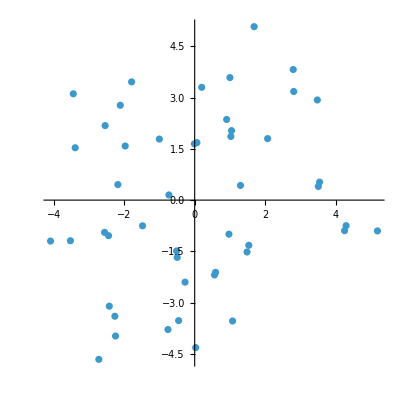

```mathematica
ListPlot[coordinatesAll, AspectRatio->1]
```

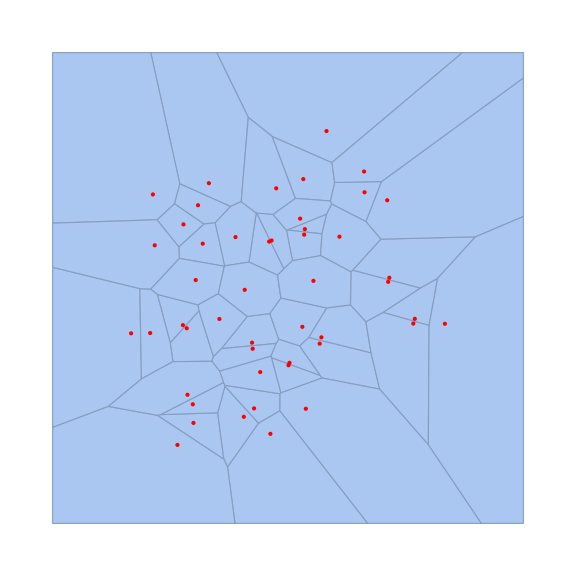

```mathematica
Show[VoronoiMesh[coordinatesAll, AspectRatio->1, ImageSize->Large],Graphics[{Red,Point[coordinatesAll]}, AspectRatio->1]]
```

```mathematica
Dimensions[mfccTx]
```

{35}

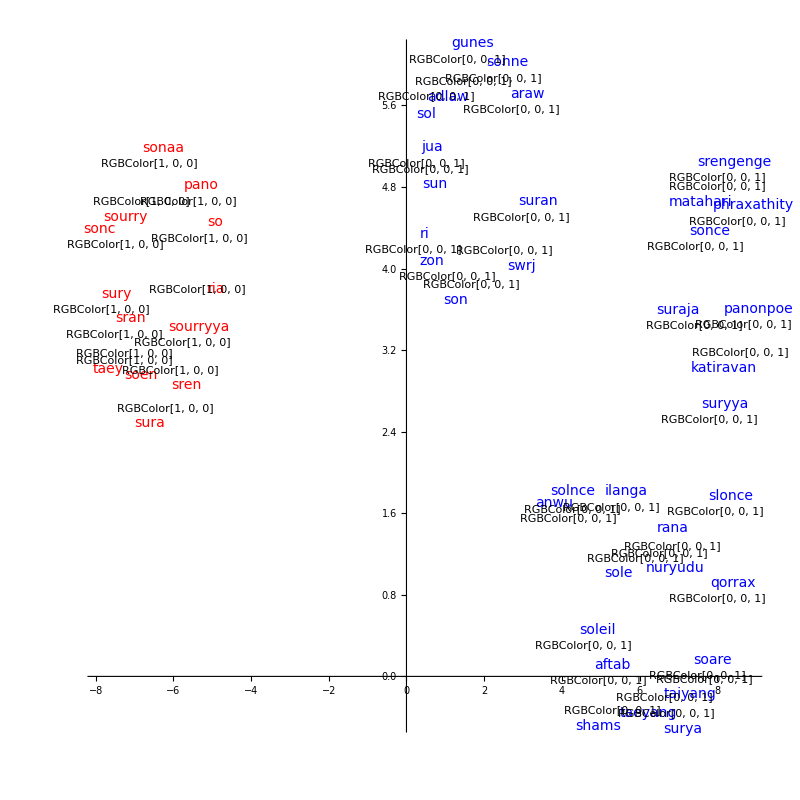

```mathematica
FeatureSpacePlot[
DeleteDuplicates[Join[
Labeled[#->Red, Style[#, Red, 14]]&/@(allPossibleWords),
Labeled[#->Blue, Style[#, Blue, 14]]&/@(testList)
]],

LabelingSize->20,Axes->True, Method->"UMAP",ImageSize->{800,800}, AspectRatio->1, FeatureExtractor->extractor
]
```

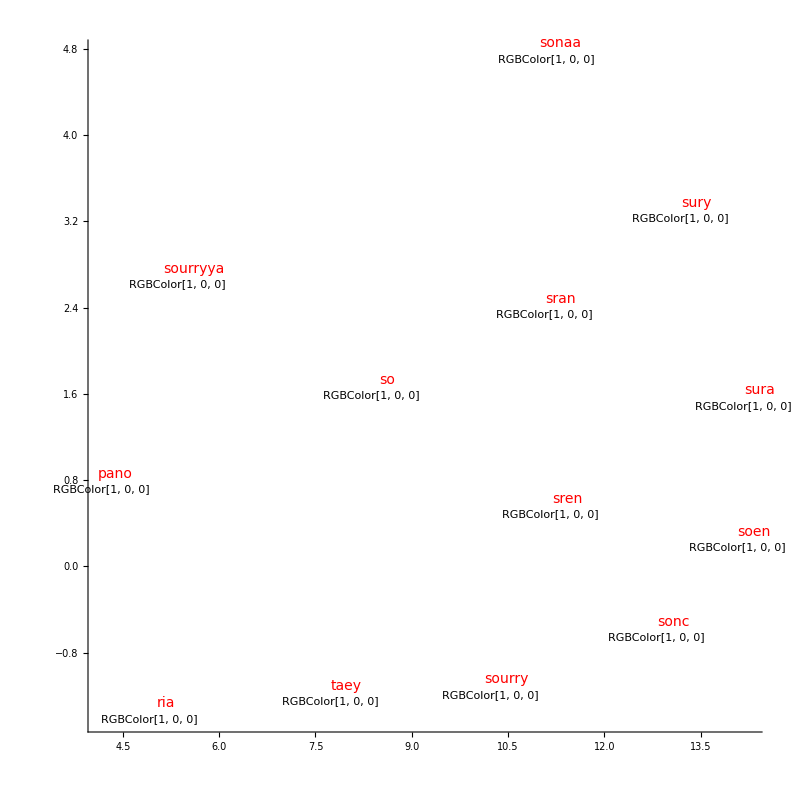

```mathematica
a=FeatureSpacePlot[
DeleteDuplicates[Join[
Labeled[#->Red, Style[#, Red, 14]]&/@(allPossibleWords)
]],

LabelingSize->20,Axes->True, Method->"UMAP",ImageSize->{800,800}, AspectRatio->1, FeatureExtractor->extractor
]
```

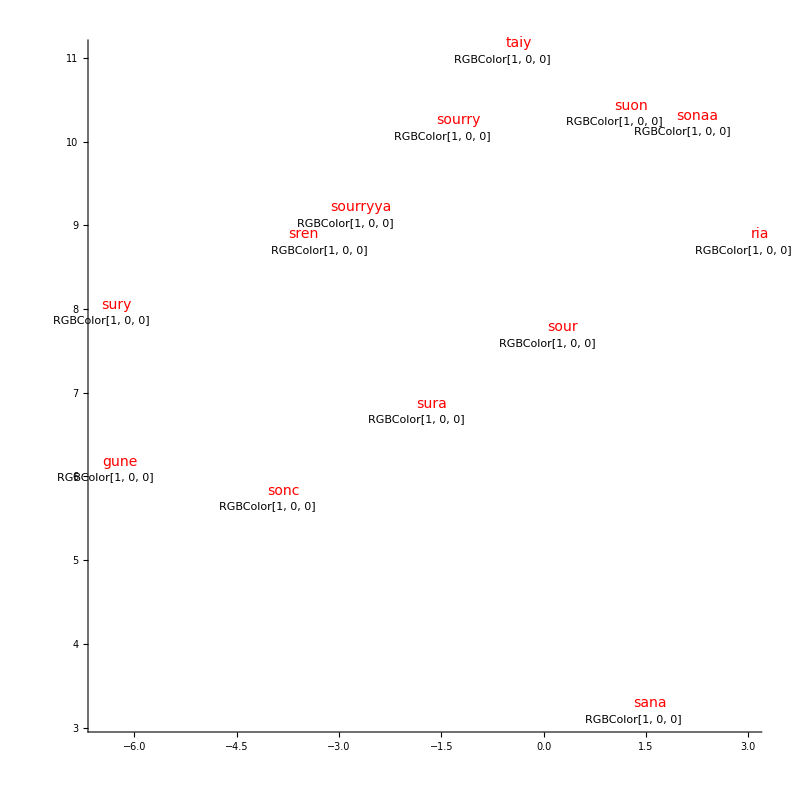

-Graphics-

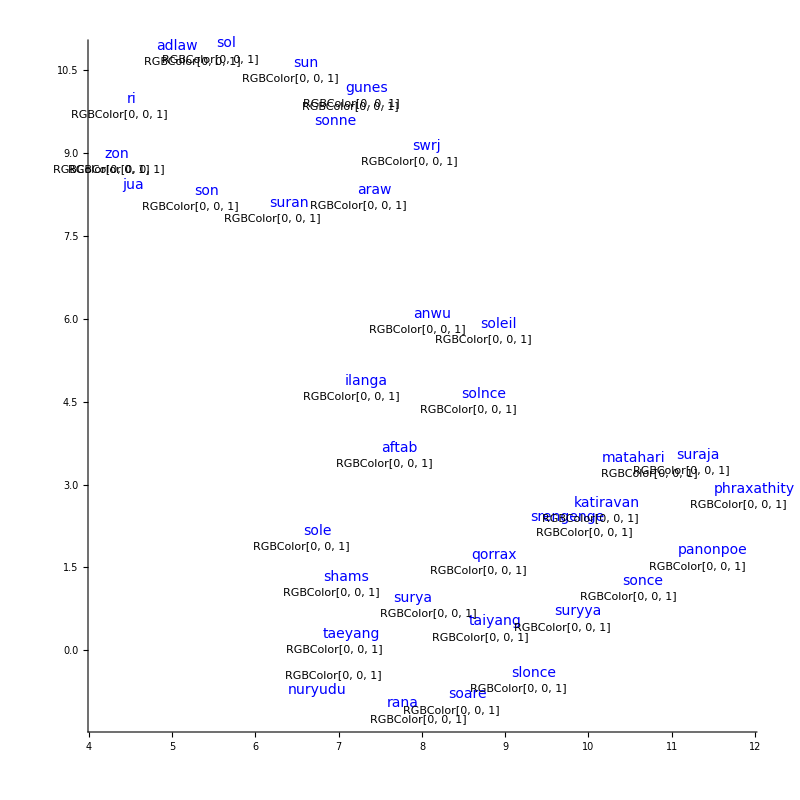

```mathematica
b=FeatureSpacePlot[
DeleteDuplicates[Join[
Labeled[#->Blue, Style[#, Blue, 14]]&/@(testList)
]],

LabelingSize->20,Axes->True, Method->"UMAP",ImageSize->{800,800}, AspectRatio->1, FeatureExtractor->extractor]
```

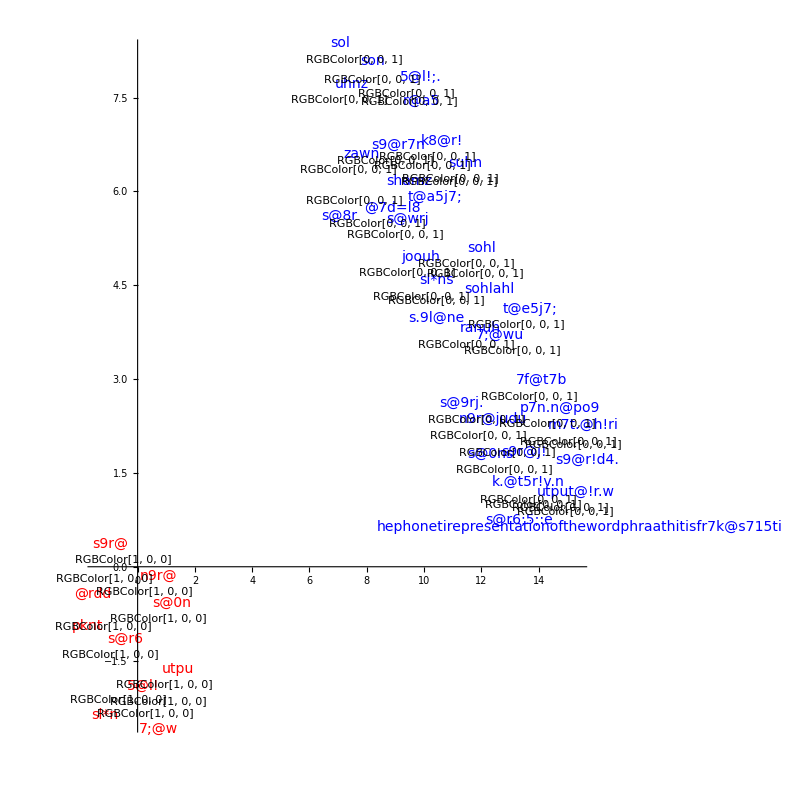

```mathematica
FeatureSpacePlot[
DeleteDuplicates[Join[
Labeled[#->Red, Style[#, Red, 14]]&/@(StringJoin[Lookup[symbolMap,#,#]&/@Characters[#]]&/@StringReplace[newAvgWordsPhonetics, "•"->""]),
Labeled[#->Blue, Style[#, Blue, 14]]&/@(StringJoin[Lookup[symbolMap,#,#]&/@Characters[#]]&/@StringReplace[ipaList, "•"->""])
]],

LabelingSize->20,Axes->True, Method->"UMAP",ImageSize->{800,800}, AspectRatio->1, FeatureExtractor->extractorPhon
]
```

## Ease of pronunciation

Now that we have a list of possibly generated words from our different methods,

```mathematica
allPossibleWords
```

{pano,ria,sonc,sren,sura,sury,taey,soen,sourryya,so,sourry,sonaa,sran}

```mathematica
pronounceabilityScore[str_String]:=Module[{knownWords,syllables,vowelCount,consonantCount,vowelConsonantPenalty,dictionaryMatch,rareClusterPenalty,normalizedLength,totalScore},rareClusterPenalty=StringCount[str,RegularExpression["[^aeiouyAEIOUY]{3,}"]];
If[rareClusterPenalty>0,Return[1000]];
knownWords=DictionaryLookup["*"];
syllables=StringCount[ToLowerCase[str],RegularExpression["[aeiouy]+"]];
dictionaryMatch=Min[EditDistance[ToLowerCase[str],#]&/@Select[knownWords,Abs[StringLength[#]-StringLength[str]]<=2&]];
normalizedLength=StringLength[str]/10.0;
vowelCount=StringCount[str,RegularExpression["[aeiouyAEIOUY]"]];
consonantCount=StringLength[str]-vowelCount;
vowelConsonantPenalty=Abs[vowelCount-consonantCount]/StringLength[str];
totalScore=syllables+dictionaryMatch/10+vowelConsonantPenalty+normalizedLength;
totalScore;
]
```

```mathematica
pronounceabilityScore[#]&/@allPossibleWords;
sortedByPronunciation = Reverse[SortBy[allPossibleWords,pronounceabilityScore]];
sortedByPronunciation
```

{taey,sury,sura,sren,sran,sourryya,sourry,sonc,sonaa,soen,so,ria,pano}

## Evaluation and Visualization

```mathematica
allPossibleWords
```

{pano,ria,sonc,sren,sura,sury,taey,soen,sourryya,so,sourry,sonaa,sran}

```mathematica
coordinatesAll=DimensionReduce[DeleteDuplicates[Join[allPossibleWords, translatedList]],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesAll;
```

```mathematica
coordinatesBase=DimensionReduce[DeleteDuplicates[translatedList],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesBase;
```

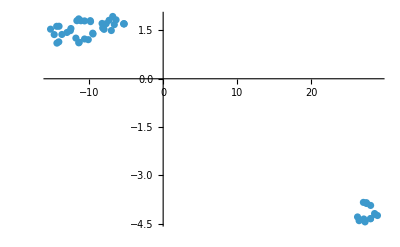

```mathematica
ListPlot[coordinatesAll]
```

```mathematica
coordinatesGen=DimensionReduce[DeleteDuplicates[allPossibleWords],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesGen;
```

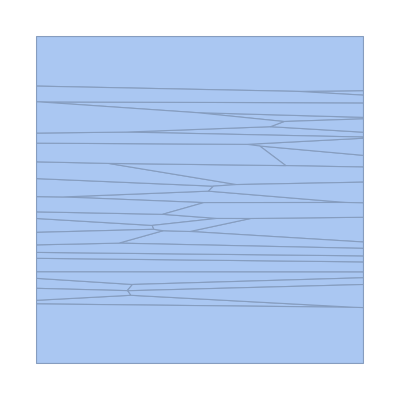

```mathematica
VoronoiMesh[coordinatesBase, AspectRatio->1]
```

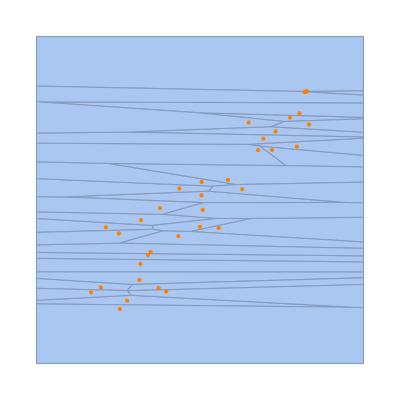

```mathematica
Show[%,Graphics[{Orange,Point[coordinatesBase]}, AspectRatio->1]]
```

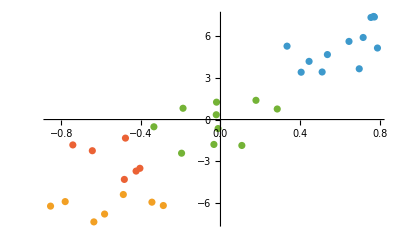

```mathematica
ListPlot[FindClusters[coordinatesBase,4,Method->"KMeans"]]
```

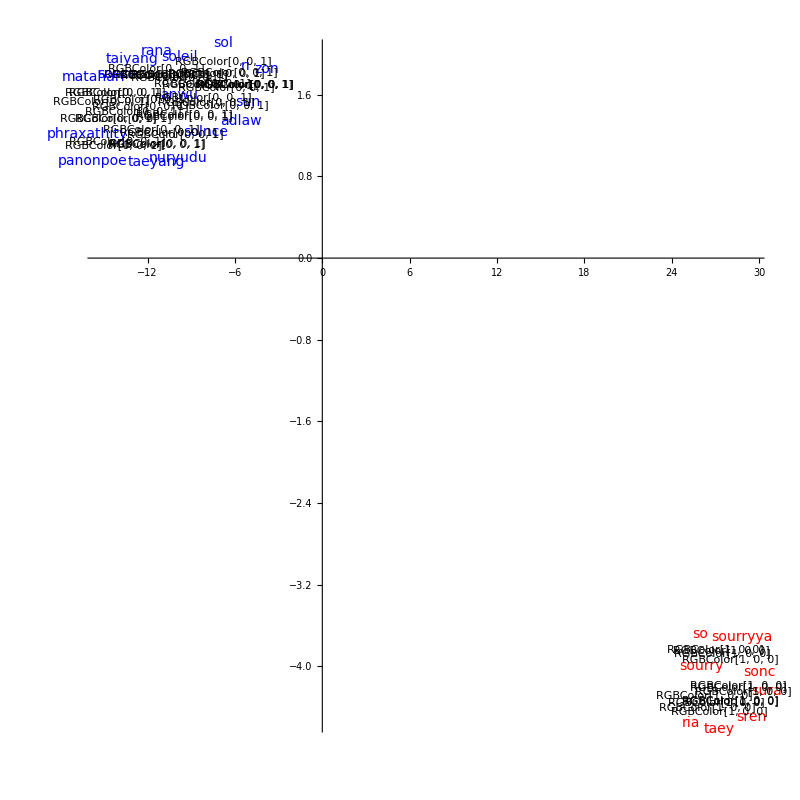

```mathematica
FeatureSpacePlot[
DeleteDuplicates[Join[
Labeled[#->Red, Style[#, Red, 14]]&/@allPossibleWords,
Labeled[#->Blue, Style[#, Blue, 14]]&/@translatedList
]],
FeatureExtractor->extractor,
LabelingSize->30,Axes->True, Method->"TSNE",ImageSize->{800,800}, AspectRatio->1
]
```

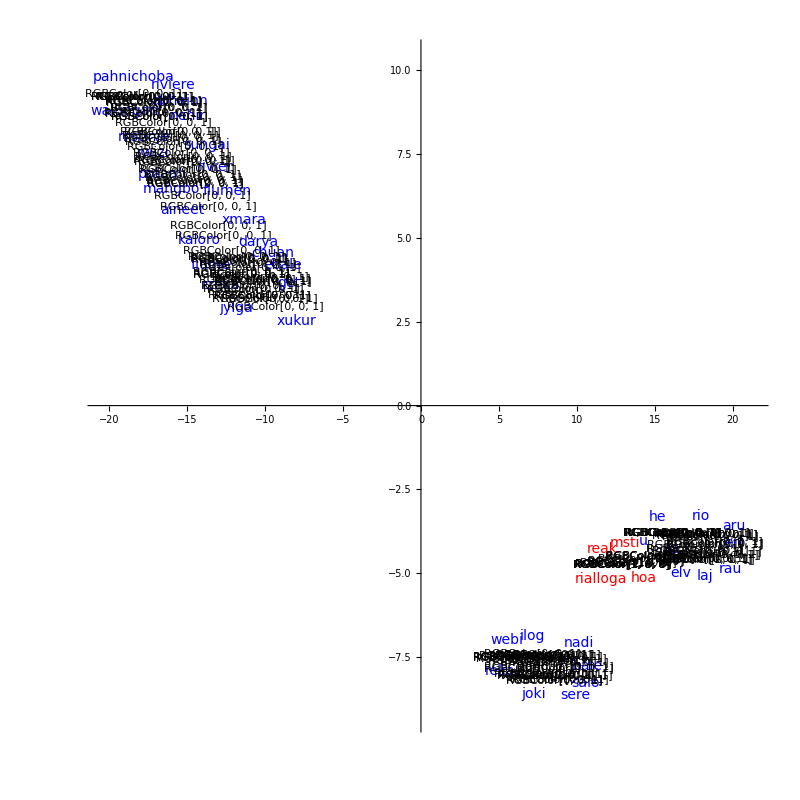

-Graphics-

## Metrics

We have some approaches which provide us with reasonable results. However, we need to quantify and visualize our newly generated words.

```mathematica
plotFitnessHeatmap[allPossibleWords]
```

plotFitnessHeatmap[{pano,ria,sonc,sren,sura,sury,taey,soen,sourryya,so,sourry,sonaa,sran}]

```mathematica
WordCloud[StringTake[allPossibleWords, 1]]
```

-Graphics-

```mathematica
plotFitnessHeatmap[allPossibleWords_List]:=Module[{fitnessValues,reshapedValues,size,wordsMatrix},
	  fitnessValues=extractor /@ allPossibleWords;
	  size=Ceiling[Sqrt[Length[fitnessValues]]];
	  reshapedValues=PadRight[Partition[fitnessValues,size,size,{1,1},{}],{size,sh`ize},None];
	  wordsMatrix=PadRight[Partition[allPossibleWords,size,size,{1,1},""],{size,size},None];
	  S 33
	]
```

```mathematica
plotFitnessHeatmap[allPossibleWords]
```

PadRight::ilsm: List of machine-sized integers expected at position 2 in PadRight[{{3.64344,4.60009,2.42819,2.83383},{2.06576,2.48795,3.49454,2.83548},{3.29537,3.69878,3.32705,4.86774},{2.88083}},{4,sh`ize},None].

33 S